Get the photon flux of generic spectrum. PPPC uses GeV. Output should be MeV to match the Fermi analysis.

```mathematica
Get["/Users/austingottfredson/Indirect-Dark-Matter-Detection/dlNdlxEW.m"];
```

```mathematica
primary="b";
j0=10^18;
sigmav0=10^-25;
```

```mathematica
dndlx[mdm_,primary_]:=With[{i:=10^xp},Table[{i mdm,10^(dlNdlxIEW[primary->"γ"][mdm,Log[10,i]])},{xp,-7,0,.1}]];
```

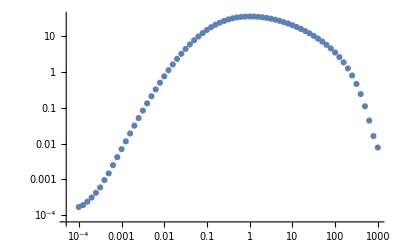

```mathematica
ListLogLogPlot[dndlx[1000,primary]]
```

photonflux will give the specfile needed to upload to the python file

```mathematica
photonflux[mdm_,primary_]:=Table[{dndlx[mdm,primary][[n,1]],1/(4 Pi)sigmav0/(2 mdm^2) dndlx[mdm,primary][[n,2]] j0},{n,1,Length[dndlx[mdm,primary]]}]
```

```mathematica
ListLogLogPlot[photonflux[1000,primary]]
```

eflux multiplies the spectrum by k (kinetic energy of photon) to get energy flux

```mathematica
eflux[mdm_,primary_]:=Table[{dndlx[mdm,primary][[n,1]],1/(4 Pi)sigmav0/(2 mdm^2) dndlx[mdm,primary][[n,2]]*dndlx[mdm,primary][[n,1]] j0},{n,1,Length[dndlx[mdm,primary]]}]
```

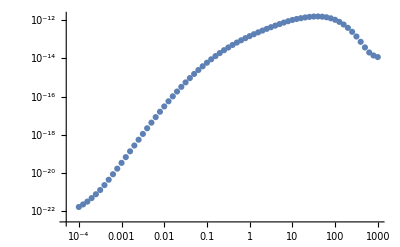

```mathematica
ListLogLogPlot[eflux[1000,primary]]
```